## Initialisation code

Choose a and b as per choice

```mathematica
a=1;
b=1;
length=10;
```

```mathematica
getM[n_,gm_,a_,b_]:=Module[{M,i,j},M=Table[0,{n},{n}];
For[i=1,i≤n,i++,
         {
           If[i==1 ,For[j=2,j≤b+1,j++,M[[i,j]]=1-gm],Unevaluated[Sequence[]]];
           If[i==n ,For[j=n-a,j≤n-1,j++,M[[i,j]]=gm],Unevaluated[Sequence[]]];
           If[2<=i≤n-b,M[[i,i+b]]=1-gm,Unevaluated[Sequence[]]];
           If[a+1<=i≤n,M[[i,i-a]]=gm,Unevaluated[Sequence[]]];
      }
      ];
{M[[1,1]]=1-gm,M[[n,n]]=gm};M]
```

```mathematica
getM[length+1,γ,a,b]//Transpose//MatrixForm
```

(1-γ | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1-γ | 0 | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1-γ | 0 | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1-γ | 0 | γ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1-γ | 0 | γ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1-γ | 0 | γ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1-γ | 0 | γ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1-γ | 0 | γ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-γ | 0 | γ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-γ | 0 | γ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-γ | γ)

```mathematica
𝒫[γ_]:=DiscreteMarkovProcess[ReplacePart[ConstantArray[0,length+1],2->1],getM[length+1,γ,a,b]//Transpose];
𝒟=.;
𝒟[γ_]:=StationaryDistribution[𝒫[γ]]
```

```mathematica
K=length;
p=0.4;
Subscript[p, 1]=0;
Subscript[p, 2]=0.8;
simply=Table[Simplify[PDF[𝒟[γ],i+1]],{i,0,length,1}];
th=.;
q[i_,γ_]:=γ p + (1-γ) Subscript[p, i];
sols=Table[qs=Table[If[i≤th,q[1,γ],q[2,γ]],{i,0,K,1}]/.th->j;
temp=simply.qs;
{j ,γ/.Solve[temp==0.5&&γ>0&&γ<1,γ]//Quiet}//Flatten,
{j ,Range[0,K]}];
```

```mathematica
toplone=Select[sols,Length[#]==3&];
```

```mathematica
{covercol,cashcol}=ColorData[97,"ColorList"]⟦{1,2}⟧;
col[x_]:=Blend[{covercol,cashcol},x]
gammastopl=Table[i,{i,0,1,0.1}];
coltopl=Table[col[1-gammastopl⟦i⟧],{i,Length[gammastopl]}];
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]}

```mathematica
q[i_,γ_]:=γ p + (1-γ) Subscript[p, i];
Pwin[γ_,th_]:=q[1,γ] ∑_(i=0)^th PDF[𝒟[γ],i+1]+q[2,γ] ∑_(i=th+1)^K PDF[𝒟[γ],i+1];
extremes={{0,Pwin[0,1]},{1,Pwin[1,1]}};
explorethresh=Range[0,5,1];
pwinlist=Table[{γ,Pwin[γ,th]},{th,explorethresh},{γ,0,1,0.01}];
```

## Plotting

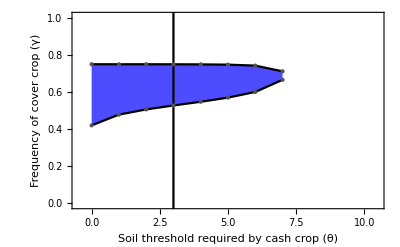

```mathematica
ListPlot[{toplone⟦All,{1,2}⟧,toplone⟦All,{1,3}⟧},PlotStyle->{Black},PlotRange->{{-0.5,K+0.5},{-0.01,1.01}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Soil threshold required by cash crop (θ)",14,Black],Style["Frequency of cover crop (γ)",14,Black]},Joined->True,Mesh->All,Filling->{1->{2}},FillingStyle->Lighter[Blue,0.3],MeshStyle->{PointSize[Large],Darker[Gray]},GridLines->{{3}, None},GridLinesStyle->Directive[{Black,Thickness[0.004]}],Method->{"GridLinesInFront"->True}]
```

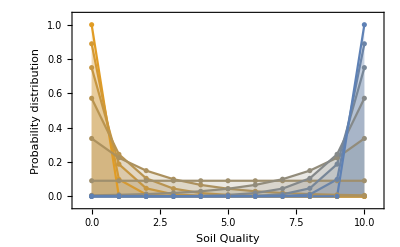

```mathematica
ListPlot[Table[{k-1,PDF[𝒟[γ],k]},{γ,gammastopl},{k,1,length+1}],PlotStyle->coltopl,(*PlotLegends->gammastopl,*)Joined->True,Mesh->All,PlotRange->{{-0.5,length+0.5},{-0.05,1.05}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Soil Quality",14,Black],Style["Probability distribution",14,Black]},Filling->Axis]
```

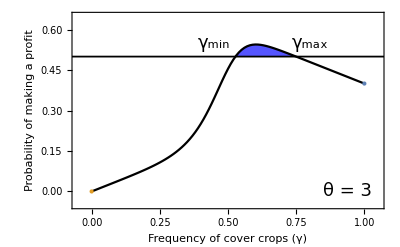

```mathematica
ListPlot[pwinlist⟦4⟧,Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Frequency of cover crops (γ)",14,Black],Style["Probability of making a profit",14,Black]},PlotStyle->Black,PlotRange->{{-0.05,1.05},{-0.05,0.65}},GridLines->{None, {0.5}},GridLinesStyle->Directive[{Black,Thickness[0.0032]}],Filling->{1-> {0.5,{None,Lighter[Blue]}}},Epilog->{PointSize[Large],cashcol,Point[extremes⟦1⟧],PointSize[Large],covercol,Point[extremes⟦2⟧],Black,Inset[Style["γ_min",18],{0.45,0.55}],Inset[Style["γ_max",18],{0.8,0.55}],Inset[Style["θ = "<>ToString[explorethresh⟦4⟧],18],{0.94,0}]},Method->{"GridLinesInFront"->True}]
```

```mathematica
Manipulate[ListPlot[pwinlist⟦j⟧,Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Frequency of cover crops (γ)",14,Black],Style["Probability of making a profit",14,Black]},PlotStyle->Black,PlotRange->{{-0.05,1.05},{-0.05,0.65}},GridLines->{None, {0.5}},GridLinesStyle->Black,Filling->{1-> {0.5,{None,Lighter[Blue]}}},Epilog->{PointSize[Large],cashcol,Point[extremes⟦1⟧],PointSize[Large],covercol,Point[extremes⟦2⟧],Black,Inset[Style["γ_min",18],{0.45,0.55}],Inset[Style["γ_max",18],{0.8,0.55}],Inset[Style["θ = "<>ToString[explorethresh⟦j⟧],18],{0.94,0}]}],{j,Range[Length[explorethresh]]}]
```